# Send queries to quantum processing units

Interact with quantum processing units

## Example Content

By utilizing the Wolfram notebook and leveraging the Wolfram quantum framework, users can engage with multiple APIs and dispatch quantum tasks. In particular, we support Amazon Braket on AWS, and IBM Quantum.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

Create a circuit:

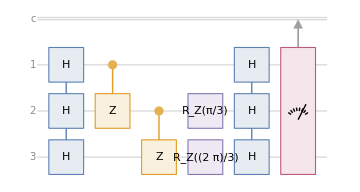

```mathematica
qc=QuantumCircuitOperator[{"H"->{1,2,3},"CZ","CZ"->{2,3},{"RZ",π/3}->2,{"RZ",2π/3}->3,"H"->{1,2,3},{1,2,3}}];
qc["Diagram"]
```

Using IBM API token, connect to IBM-quantum using service connection:

```mathematica
ibm=ServiceConnect["IBMQ"]
```

ServiceObject[…]

Transform the quantum circuit into Qiskit and traspile it:

```mathematica
qiskit=qc["Qiskit"]["Transpile"];
```

Turn the qiskit object into bytes by specifying the corresponding provider and backend on IBM system:

```mathematica
qpy=BaseEncode@qiskit["QPY","Provider"->"IBMProvider","Backend"->"ibmq_quito"];
```

Send the circuit to an IBM QPU:

```mathematica
ibm["RunCircuit",{"QPY"->qpy,"Backend"->"ibmq_belem"}]
```

Check the job’s status:

```mathematica
ibm["JobStatus",{"JobID"->"chng53laqbbvbu6o1qgg"}]
```

Get the results:

```mathematica
ds=ibm["JobResults",{"JobID"->"chng53laqbbvbu6o1qgg"}]
```

Given counts in the results, find the corresponding probabilities:

```mathematica
qpuResults=N@Normalize[Values@Normal[ds["results",All,"data","counts"]][[1]],Total]
```

{0.11775,0.177,0.1055,0.15975,0.14825,0.073,0.16425,0.0545}

Calculate results from Wolfram quantum framework:

```mathematica
results=qc[]["Probabilities"]
```

<|000→1/16,001→3/16,010→1/16,011→3/16,100→3/16,101→1/16,110→3/16,111→1/16|>

Connect to AWS using your credentials (using Access Key ID, and Secret Access Key), and execute S3:

```mathematica
s3=ServiceExecute["AWS","GetService",{"Name"->"S3"}]
```

ServiceObject[…]

Execute Amazon Braket on AWS:

```mathematica
braket=ServiceExecute["AWS","GetService",{"Name"->"Braket"}]
```

ServiceObject[…]

Fetch available devices:

```mathematica
devices=braket["SearchDevices","Filters"->{}]["Devices",All]
```

Pick IonQ Harmony as a QPU:

```mathematica
ionq=devices[3,MapAt[ImportString[#,"RawJSON"]&,"DeviceCapabilities"]]
```

Transform the quantum circuit into Qiskit and finds it QASM using AWSProvider for IonQ Harmony:

```mathematica
qasm=qc["Qiskit"]["QASM","Provider"->"AWSBraket","Backend"->"Harmony"]
```

OPENQASM 3.0;
qubit[3] q;
h q[0];
h q[1];
h q[1];
cnot q[0], q[1];
h q[0];
h q[1];
h q[2];
h q[2];
cnot q[1], q[2];
rz(1.0471975511965976) q[1];
h q[1];
h q[2];
rz(2.0943951023931953) q[2];
h q[2];
#pragma braket result probability q[2], q[0]
#pragma braket result probability q[1]
#pragma braket result probability q[0], q[2]

Send a quantum task to IonQ Harmony

```mathematica
taskIonQ=braket["CreateQuantumTask",
"DeviceArn"->ionq["DeviceArn"],
"DeviceParameters"->{},
"OutputS3Bucket"->"amazon-braket-wolfram-mads","OutputS3KeyPrefix"->"tasks",
"Shots"->100,"Action"-><|"braketSchemaHeader"-><|"name"->"braket.ir.openqasm.program","version"->"1"|>,
"source"->qasm|>,
"ValidateRequest"->False,"RequestRegion"->"us-east-1"]
```

Check the status of the task:

```mathematica
braket["GetQuantumTask","QuantumTaskArn"->taskIonQ["QuantumTaskArn"],"RequestRegion"->"us-east-1"]
```

Find the output directory on S3:

```mathematica
outputPathIONQ=braket["GetQuantumTask","QuantumTaskArn"->taskIonQ["QuantumTaskArn"],"RequestRegion"->"us-east-1"]["OutputS3Directory"]
```

tasks/7e0f331a-0868-4831-9027-6262afacdc14

Get the results:

```mathematica
resultsIonQ=KeySort[ImportByteArray[s3["GetObject","Bucket"->"amazon-braket-wolfram-mads","Key"->FileNameJoin[{outputPathIONQ,"results.json"}],"RequestRegion"->"us-east-1"]["Body"],"RawJSON"]["measurementProbabilities"]]
```

<|000→0.07,001→0.2,010→0.09,011→0.17,100→0.17,101→0.04,110→0.16,111→0.1|>

Make sure zero probabilities are also included:

```mathematica
resultsIonQ=Join[AssociationThread[StringJoin/@Tuples[{"0","1"},3],0],resultsIonQ]
```

<|000→0.07,001→0.2,010→0.09,011→0.17,100→0.17,101→0.04,110→0.16,111→0.1|>

Visualize results:

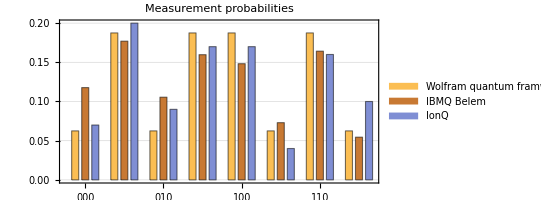

```mathematica
BarChart[Transpose[{Values[results],qpuResults,Values@resultsIonQ}],ChartLegends->{"Wolfram quantum framwork","IBMQ Belem","IonQ"},ChartLabels->{Keys[results],None},Frame->True,GridLines->Automatic,AspectRatio->1/2,PlotLabel->"Measurement probabilities"]
```

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

-Graphics-

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

Quantum processing units

Quantum circuits

Quantum measurement

Probability

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.